# Study Hour

## Theory

```mathematica
h = time for study a new chapter
r = rate of revision
n , h r^(n+1)< (1/12)[hours] ⇒ h -> 0
n = Log[ r,1/(h 12)]//Floor
m = number of chapters
```

```mathematica
a[1]=h;
a[2]=h+h r
a[3]=h+h r +h r^2
a[n]= h Sum[r^k,{k,0,n-1}]
a[n+1]=h Sum[r^k,{k,0,n}]
a[n+2]=a[n+1]
a[m]=a[n+1]
a[m+1]=h  Sum[r^k,{k,1,n}]
a[m+2]=h r^2 Sum[r^k,{k,2,n}]
a[m+n-1]= h r^(n-1)(1+r)
a[m+n]=h r^n
a[m+n+1]=0
```

```mathematica
t[m,d]=time for study m-th chapter on d-th day
```

```mathematica
t[1,1]=h
t[1,2]=h r
t[1,n]=h r^n
t[2,1]=0
t[2,2]=h
t[2,3]=h r
t[2,n]=h r^(n-2)
```

```mathematica
(* Define t, when  l>d, not lesson for chaper d, t = 0, or n = d-l >0, t = 0, or l>m, t=0 *)
t[l_,d_]:=h r^(d-l)/.h_/;((d-l<0) ||( d-l>n )||l>m)->0;
a[i_]:=Sum[t[l,i],{l,1,i}];
```

```mathematica
Clear[t]
```

```mathematica
a[n]
```

(h (-1+r^n))/(-1+r)

```mathematica
(* Notics *)
r^x= Exp[ Log [r] x]
(1-r^x)/(1-r)==(1- Exp[ Log[r]x])1/(1-r)
(* Since r < 1, Log[r] < 0 , Thus, the function is (1- Exp[-x]) *)
```

```mathematica
D[(1-r^x)/(1-r),x]
```

-(r^x Log[r])/(1-r)

```mathematica
Manipulate[Plot[{(1-r^x)/(1-r),-(r^x Log[r])/(1-r)},{x,0,10},PlotRange->{0,All},PlotStyle->{Red, Blue}],{{r,0.5},0,1}]
```

```mathematica
b[1]=a[m+1]=h r + h r^2+...+ h r^n+(h r^(n+1)-> 0)=a[m]-h
b[2]=a[m+2]=h r^2+...+h r^n=a[m+1]-h r
b[3]=a[m+2]-hr^2
```

```mathematica
b[d_]:=h Sum[r^k,{k,d,n}]
```

```mathematica
b[d]
```

(h (-r^d+r^(1+n)))/(-1+r)

```mathematica
r^x=Exp[Log[r] x]
(r^(x-m)-r^(1+n))/(1-r)= 1/(1-r)(Exp[Log[r] (x-m)]-r^(1+n))
(* Since r < 1, Log[r] < 0 , Thus, the function is Exp[-x] *)
(*  r^n > 1/(12 h), thus n is depend on r *)
```

```mathematica
D[(r^(x-m)-r^(1+n))/(1-r),x]
```

(r^(-m+x) Log[r])/(1-r)

```mathematica
(* Notics that it does not depend on n *)
```

```mathematica
Manipulate[Plot[{(r^(x-m)-r^(1+n))/(1-r),- (r^(-m+x) Log[r])/(1-r)},{x,0,10},PlotRange->{0,All},PlotStyle->{Red, Blue}],{{r,0.5},0,1},{{m,4},1,10,1},{{n,3},1,10,1}]
```

```mathematica
Manipulate[Plot[{(r^(x-m)-r^(1+n))/(1-r), (1-r^x)/(1-r)},{x,0,m+n+2},PlotRange->{0,1/(1-r)},PlotStyle->{Red, Blue}],{{r,0.5},0,1},{{m,4},1,10,1},{{n,3},1,10,1}]
```

```mathematica
(* Charging and Discharge curve *)
```

## Example

```mathematica
Clear[h,r,n,m,t,a,b,day,Steady]
```

```mathematica
1/12//N
Rev=Table[{r,Log[r,1/(h 12)]},{r,0.1,0.9,0.05}];
Rev//TableForm
DRev=Table[Rev[[i+1,2]]-Rev[[i,2]],{i,1,16}]
```

0.0833333

0.1 | 1.07918
0.15 | 1.30983
0.2 | 1.54396
0.25 | 1.79248
0.3 | 2.06392
0.35 | 2.36698
0.4 | 2.71192
0.45 | 3.11194
0.5 | 3.58496
0.55 | 4.1565
0.6 | 4.86449
0.65 | 5.76835
0.7 | 6.96687
0.75 | 8.63768
0.8 | 11.1359
0.85 | 15.29
0.9 | 23.5848

{0.23065,0.234128,0.248522,0.271441,0.303056,0.344941,0.400019,0.473024,0.571533,0.707996,0.903859,1.19852,1.67082,2.49823,4.15404,8.29485}

```mathematica
h=1;
r=1/2;
m=6;
n=Log[ r,1/(h 12)]//Floor
Table[h r^k//N,{k,0,n+1}]
(* time for finish each chapter *)
Sum[h r^k,{k,0,n}]//N
m%
(* day for study *)
day=m+n
(* Day for steady study *)
Steady=m-n
(* Define t, when  l>d, not lesson for chaper d, t = 0, or n = d-l >0, t = 0, or l>m, t=0 *)
t[l_,d_]:=h r^(d-l)/.h_/;((d-l<0) ||( d-l>n )||l>m)->0;
a[i_]:=Sum[t[l,i],{l,1,i}];
```

3

{1.,0.5,0.25,0.125,0.0625}

1.875

11.25

9

3

```mathematica
Table[t[l,d]//N,{l,1,m+1},{d,1,day+2}]//TableForm
```

1. | 0.5 | 0.25 | 0.125 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0.5 | 0.25 | 0.125 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0.5 | 0.25 | 0.125 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0.5 | 0.25 | 0.125 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 1. | 0.5 | 0.25 | 0.125 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1. | 0.5 | 0.25 | 0.125 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.

11.25

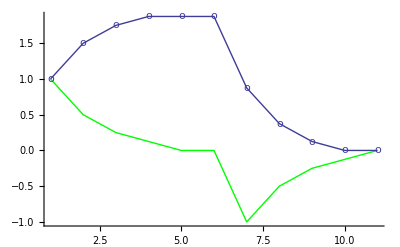

```mathematica
L=Table[a[i]//N,{i,1,day+2}];
(* Total hours of study *)
Sum[a[i],{i,1,20}]//N
DL=Table[(a[i+1]-a[i])//N,{i,0,day+1}];
Show[ListPlot[DL,Joined->True,PlotStyle->Green],
ListPlot[L,Joined->True,PlotMarkers->o]
]
```

```mathematica
(* Compare *)
Manipulate[Show[
Plot[{(rr^(x-mm)-rr^(1+nn))/(1-rr), (1-rr^x)/(1-rr)},{x,0,day+2},PlotRange->{Min[DL],1/(1-rr)},PlotStyle->{{Red,Dashed},{ Blue,Dashed}}],
ListPlot[L,Joined->True,PlotStyle->{Purple},PlotMarkers->o],
ListPlot[DL,Joined->True,PlotStyle->Green]
],{{rr,r},0,1},{{mm,m},1,10,1},{{nn,n},1,10,1}]
```

## Extra 1 ( differenrt difficult )

```mathematica
Clear[h,r,n,m,t,a,b,day,steady]
```

```mathematica
(* when the difficult increase for later chapter, the hour spend on it will be longer *)
(* h will be a function of chapter *)
```

```mathematica
(* n still obey the general equaltion *)
h[l] r^n[l]> 1/12
(* but every chapter has differnt n *)
(* n = n[l] *)
```

```mathematica
(* Baisc Parameter *)
h[l_]:=0.5 l^(1/3);
r=1/2;
m=6;
```

```mathematica
(* number of day for revision of l-chapter*)
n[l_]:=Log[ r,1/(h[l] 12)]//Floor
Table[n[i],{i,1,m+2}]
```

{2,2,3,3,3,3,3,3}

```mathematica
Table[h[i] r^k//N,{i,1,m},{k,0,n[i]+1}]//TableForm
(* time for finish each chapter *)
fin[l_]:=Sum[h[l] r^k,{k,0,n[l]}]//N
Table[fin[i],{i,1,m}]
(* Total Time of study *)
Sum[fin[i],{i,1,m}]
```

0.5 | 0.25 | 0.125 | 0.0625 | 
0.629961 | 0.31498 | 0.15749 | 0.0787451 | 
0.721125 | 0.360562 | 0.180281 | 0.0901406 | 0.0450703
0.793701 | 0.39685 | 0.198425 | 0.0992126 | 0.0496063
0.854988 | 0.427494 | 0.213747 | 0.106873 | 0.0534367
0.90856 | 0.45428 | 0.22714 | 0.11357 | 0.056785

{0.875,1.10243,1.35211,1.48819,1.6031,1.70355}

8.12438

```mathematica
(* Total day for study *)
day = m+n[m]
```

9

```mathematica
t[l_,d_]:=h[l] r^(d-l)/.h_/;((d-l<0) ||( d-l>n[l] )||l>m)->0;
a[i_]:=Sum[t[l,i],{l,1,i}];
```

```mathematica
Table[t[l,d]//N,{l,1,m+1},{d,1,day+2}]//TableForm
```

0.5 | 0.25 | 0.125 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.629961 | 0.31498 | 0.15749 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.721125 | 0.360562 | 0.180281 | 0.0901406 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.793701 | 0.39685 | 0.198425 | 0.0992126 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.854988 | 0.427494 | 0.213747 | 0.106873 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.90856 | 0.45428 | 0.22714 | 0.11357 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.

8.12438

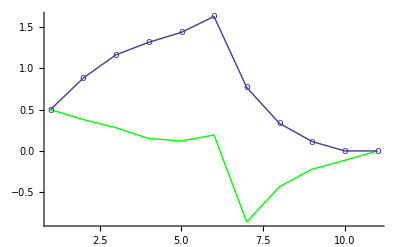

```mathematica
L=Table[a[i]//N,{i,1,day+2}];
(* Total hours of study *)
Sum[a[i],{i,1,20}]//N
DL=Table[(a[i+1]-a[i])//N,{i,0,day+1}];
Show[ListPlot[DL,Joined->True,PlotStyle->Green],
ListPlot[L,Joined->True,PlotMarkers->o]
]
```

## Extra 2 ( Fix Max hours of study )

```mathematica
(* at the beginning, the chapter learned increse, so hour increase *)
```

```mathematica
(* Given the total hours of study *)
(* Found out the day that needed to study *)
(* and the disturbution of stuyd time *)
```